# Figure 2

Clicking Run all evaluates the whole notebook from top to bottom . Some computations may take a while, so please wait until all cells have finished running .

```mathematica
Button["Run all",
With[{nb=ButtonNotebook[]},
FrontEndTokenExecute[nb,"EvaluateNotebook"];
SelectionMove[nb,After,Notebook]
]
]
```

Run all

```mathematica
ClearAll["Global`*"];
```

```mathematica
σnlList={{29/20,61/25},{4,21/20,241/100},{36/25,321/100,67/25,38/25}};
L1=Length[σnlList];maxN=100;
samples=10^4;
ts=Table[i,{i,2,maxN,4}];
mx=Length[ts];
seed=SeedRandom[3];
res=Table[0,{mx}];
pValues=Table[0,{mx}];
list=Table[0,{3}];
For[j=1,j<=Length[list],j++,
σs=σnlList[[j]];
L1=Length[σs];
For[n=1,n<=mx,n++,
N1=ts[[n]];
μ1=N1(√(π/2))^L1(∏_(l=1)^L1 σs[[l]]);(*mean*)
σ1=N1((∏_(l=1)^L1 (((4-π)/2)σs[[l]]^2+(√(π/2)σs[[l]])^2))-∏_(l=1)^L1 (√(π/2)σs[[l]])^2);(*variance*)
spr1=(∑_(i=1)^N1 (∏_(j=1)^L1 RandomVariate[RayleighDistribution[σs[[j]]],samples]));
pValues[[n]]={N1,KolmogorovSmirnovTest[RandomVariate[NormalDistribution[μ1,√σ1],samples],spr1,"TestStatistic",SignificanceLevel->0.05]};
];
list[[j]]=pValues;
];
```

```mathematica
SeedRandom[1234];
Lns=ConstantArray[{1,2,3,4},25]//Flatten;
σnls=Table[RandomInteger[{10,400},Lns[[i]]]/100,{i,Length[Lns]}];
σt=Apply[Times,σnls,{1}];
σns=Table[1/(σt[[i]](√2)^Lns[[i]]),{i,Length[Lns]}];
ns=Table[i,{i,2,100,2}];
```

```mathematica
samples=10^4;
seed=SeedRandom[3];
listinid=Table[0,{Length[ns]}];
mus=Table[0,{Length[ns]}];
sigmas=Table[0,{Length[ns]}];
For[j=1,j<=Length[ns],j++,
σs=σnls[[;;ns[[j]]]];
N1=Length[σs];
mus[[j]]=∑_(k=1)^N1 (√(π/2))^Length[σs[[k]]](∏_(l=1)^Length[σs[[k]]] σs[[k,l]]);(*mean*)
sigmas[[j]]=√(∑_(k=1)^N1 ((∏_(l=1)^Length[σs[[k]]] (((4-π)/2)σs[[k,l]]^2+(√(π/2)σs[[k,l]])^2))-∏_(l=1)^Length[σs[[k]]] (√(π/2)σs[[k,l]])^2));(*standar deviation*)
spr1=(∑_(i=1)^N1 (∏_(j=1)^Length[σs[[i]]] RandomVariate[RayleighDistribution[σs[[i,j]]],samples]));
listinid[[j]]={N1,KolmogorovSmirnovTest[RandomVariate[NormalDistribution[mus[[j]],sigmas[[j]]],samples],spr1,"TestStatistic",SignificanceLevel->0.05]};
];
listinid=Table[listinid[[i]],{i,1,Length[listinid],2}];
```

```mathematica
(* sum inid, products inid, number of products is the same *)
SeedRandom[1234];
Lnsnew=Table[Table[i,{100}],{i,2,4}];
σnlsSame=Table[Table[RandomInteger[{10,400},Lnsnew[[j,i]]]/100,{i,Length[Lnsnew[[j]]]}],{j,1,Length[Lnsnew]}];
σtnew=Table[Apply[Times,σnlsSame[[i]],{1}],{i,1,Length[Lnsnew]}];
σnsnew=Table[Table[1/(σtnew[[j,i]](√2)^Lnsnew[[j,i]]),{i,Length[Lnsnew[[j]]]}],{j,1,Length[Lnsnew]}];
ns=Table[i,{i,2,100,2}];
samples=10^4;
seed=SeedRandom[3];
aux=Table[0,{Length[ns]}];
mus=Table[0,{Length[ns]}];
sigmas=Table[0,{Length[ns]}];
listinidNew=Table[0,{Length[Lnsnew]}];
For[l=1,l<=Length[Lnsnew],l++,
var=σnlsSame[[l]];
For[j=1,j<=Length[ns],j++,
σs=var[[;;ns[[j]]]];
N1=Length[σs];
mus[[j]]=∑_(k=1)^N1 (√(π/2))^Length[σs[[k]]](∏_(l=1)^Length[σs[[k]]] σs[[k,l]]);(*mean*)
sigmas[[j]]=√(∑_(k=1)^N1 ((∏_(l=1)^Length[σs[[k]]] (((4-π)/2)σs[[k,l]]^2+(√(π/2)σs[[k,l]])^2))-∏_(l=1)^Length[σs[[k]]] (√(π/2)σs[[k,l]])^2));(*standar deviation*)
spr1=(∑_(i=1)^N1 (∏_(j=1)^Length[σs[[i]]] RandomVariate[RayleighDistribution[σs[[i,j]]],samples]));
aux[[j]]={N1,KolmogorovSmirnovTest[RandomVariate[NormalDistribution[mus[[j]],sigmas[[j]]],samples],spr1,"TestStatistic",SignificanceLevel->0.05]};
];
listinidNew[[l]]=aux;
];
listinidNew=Table[Table[listinidNew[[k,i]],{i,1,Length[listinidNew[[k]]],2}],{k,1,Length[listinidNew]}];
```

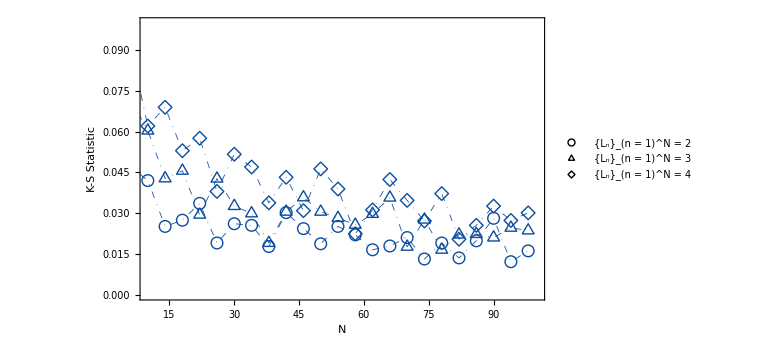

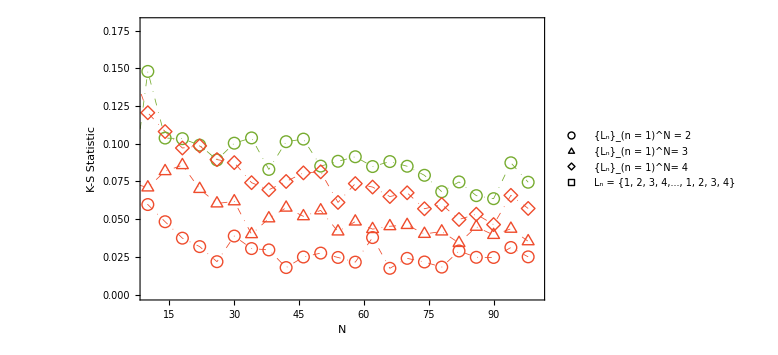

```mathematica
col1=RGBColor["#0C4D9F"]; col2=RGBColor["#EF4C2D"];col3=RGBColor["#77AC30"];col4=RGBColor["#67BC45"];
KS=ListLinePlot[{list[[1]],list[[2]],list[[3]]},PlotStyle->{{col1,DotDashed,Thickness[0.001]},{col1,DotDashed,Thickness[0.001]},{col1,DotDashed,Thickness[0.001]},{col2,DotDashed,Thickness[0.001]},{col2,DotDashed,Thickness[0.001]},{col2,DotDashed,Thickness[0.001]},{col3,DotDashed,Thickness[0.001]}},PlotRange->{{10,100},{0,0.1}},ImageSize->Large,PlotMarkers->{{"○",12},{"△",14},{"◇",14},{"○",12},{"△",14},{"◇",14},{"□",14}},Frame-> True,FrameStyle->Directive[Black,18,FontFamily-> "Times"],FrameLabel->{"N","K-S Statistic"},PlotLegends->Placed[LineLegend[{Black,Black,Black,Black,Black,Black,Black},{"{L_n}_(n = 1)^N = 2","{L_n}_(n = 1)^N = 3","{L_n}_(n = 1)^N = 4"},Joined->False,LegendMarkers->{{"○",17},{"△",20},{"◇",20},{"□",20}},LabelStyle->{Black,17,FontFamily-> "Times"},LegendLayout->{"Column",2}],{0.74,0.84}]]
KS2=ListLinePlot[{listinidNew[[1]],listinidNew[[2]],listinidNew[[3]],listinid},PlotStyle->{{col2,DotDashed,Thickness[0.001]},{col2,DotDashed,Thickness[0.001]},{col2,DotDashed,Thickness[0.001]},{col3,DotDashed,Thickness[0.001]}},PlotRange->{{10,100},{0,0.18}},ImageSize->Large,PlotMarkers->{{"○",12},{"△",14},{"◇",14},{"○",12},{"△",14},{"◇",14},{"□",14}},Frame-> True,FrameStyle->Directive[Black,18,FontFamily-> "Times"],FrameLabel->{"N","K-S Statistic"},PlotLegends->Placed[LineLegend[{Black,Black,Black,Black,Black,Black,Black},{"{L_n}_(n = 1)^N = 2","{L_n}_(n = 1)^N= 3","{L_n}_(n = 1)^N= 4","L_n = {1, 2, 3, 4,..., 1, 2, 3, 4}"},Joined->False,LegendMarkers->{{"○",17},{"△",20},{"◇",20},{"□",20}},LabelStyle->{Black,12,FontFamily-> "Times"},LegendLayout->{"Column",2}],{0.74,0.84}]]
```